```mathematica
DiffurStruc[func_,arg_,cprFunc_,ccur_]:={func'[arg]-ccur-cprFunc[func[arg]]==0};
DiffurIni[func_,InitialPoint_,InitialValue_]:={func[InitialPoint]==InitialValue};
Diffur[func_,arg_,cprFunc_,ccur_,InitialPoint_,InitialValue_]:=Flatten[
{DiffurStruc[func,arg,cprFunc,ccur],DiffurIni[func,InitialPoint,InitialValue]}];
```

```mathematica
CommonCPR[ccur_, cprFunc_, InitialPoint_,InitialValue_, {arg_,lowRange_,upperRange_}]:=
NDSolve[Diffur[γ,arg,cprFunc,ccur,InitialPoint,InitialValue],γ[arg],{arg,lowRange,upperRange}];
```

```mathematica
solution[ccur_, cprFunc_]:=Flatten[γ[t]/.CommonCPR[ccur, cprFunc,0,0,{t,0,1000π}]];
```

```mathematica
plots=Table[Plot[{(solution[i,(Sin[#]+a Sin[2#])&]/.t->1000π)/(1000π),i},{i,0,10}],{a,0,5,0.1}];
```

```mathematica
Export["F:\\Google Disk\\Учебные материалы\\Физтех\\Наука\\plot.pdf",Show[plots,ImageSize->Large]]
```

F:\Google Disk\Учебные материалы\Физтех\Наука\plot.pdf

```mathematica
Clear[result];result=ParallelTable[{{Flatten[(solution[i,(Sin[#]+a Sin[2#])&]/.t->3000)/3000][[1]],i},a},{a, 0,5,0.5},{i,-10,10,0.1}]
```

{{{{-9.95,-10.},0.},{{-9.84948,-9.9},0.},{{-9.74893,-9.8},0.},{{-9.6484,-9.7},0.},{{-9.54783,-9.6},0.},{{-9.44729,-9.5},0.},{{-9.34673,-9.4},0.},{{-9.24616,-9.3},0.},185,{{9.24616,9.3},0.},{{9.34673,9.4},0.},{{9.44729,9.5},0.},{{9.54787,9.6},0.},{{9.6484,9.7},0.},{{9.74893,9.8},0.},{{9.84947,9.9},0.},{{9.95,10.},0.}},9,{{{1},5.},199,{1}}}
 |  |  |  |

```mathematica
LoadResults[path_String]:=Module[{param}, 

param=Flatten[Map[Flatten[#]&,Import[path<>"\\currents.xls","XLS"]]];
Map[Import[path<>"\\plot"<>ToString[#]<>".xls","XLS"]&,param]];
```

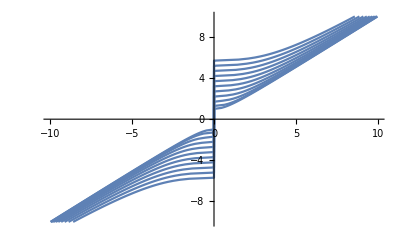

```mathematica
Map[ListLinePlot[#]&,LoadResults["F:\\Google Disk\\Учебные материалы\\Физтех\\Наука\\computation\\results\\result1"]]//Show
```